## Exercises

Q2: Integrate the expression f(x) = sin(x) e^-x, and then take its derivative.

Clear the variables:

```mathematica
Clear[f,F,PrimeF]
```

Define the function:

```mathematica
f[x_]:=Sin[x] Exp[-x]
```

Integrate the function:

```mathematica
F[x_]:=Integrate[f[t],{t,0,x}]
```

Derivate it:

```mathematica
PrimeF[w_]=FullSimplify[D[F[w],w]]
```

ⅇ^-w Sin[w]

Plot it:

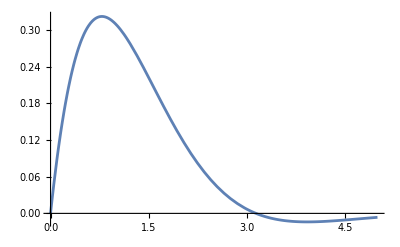

```mathematica
Plot[PrimeF[x],{x,0,5}]
```

Q3: Solve the equation  x ln(x) - 3 x + 10 = 6, both symbolically and numerically.

```mathematica
SolSym:=Solve[Reduce[x Log[x]-3x+10==6,x]]
```

Solutions:

```mathematica
SolSym[[1,1,2]]
SolSym[[2,1,2]]
```

ⅇ^(3+ProductLog[-4/ⅇ^3])

ⅇ^(3+ProductLog[-1,-4/ⅇ^3])

Numerical solutions:

```mathematica
Sol:=NSolve[Reduce[x Log[x]-3x+10==6,x]]

SolX1= Sol[[1,1,2]]
SolX2= Sol[[2,1,2]]
```

15.5229

1.56883

Q4: Solve the following initial-value problem using both DSolve and NDSolve. Compare your answers by plotting them.

	y’’(x) - x y(x) = 0
	y(0) = 1
	y’(0) = - 3^(1/3)Gamma(2/3)/Gamma(1/3)

{{y[x]→3^(2/3) AiryAi[x] Gamma[2/3]}}

{{y→InterpolatingFunction[…]}}

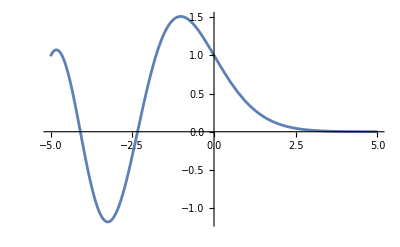

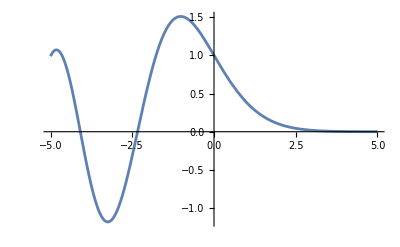

```mathematica
Clear[y,gammaFactor,solAnalitica,solNumerica]

eq:=y''[x]-x y[x]==0;

gammaFactor:=(3^(1/3) Gamma[2/3])/Gamma[1/3]

solAnalitica=DSolve[{eq,y[0]==1,y'[0]==-gammaFactor},y[x],x]

solNumerica=NDSolve[{eq,y[0]==1,y'[0]==-gammaFactor},y,{x,-10,100}]

Plot[{y[x]/. solAnalitica[[1]]},{x,-5,5}]

Plot[Evaluate[y[x]/. solNumerica],{x,-5,5}]
```